```mathematica
Вариант 7
```

```mathematica
a) lim_(n->∞) ((1+3+5+...+(2n-1))/(n+3)-n)=lim_(n->∞) (n^2/(n+3)-(n^2+3n)/(n+3))=lim_(n->∞) (-3/(1+3/n))=-3
```

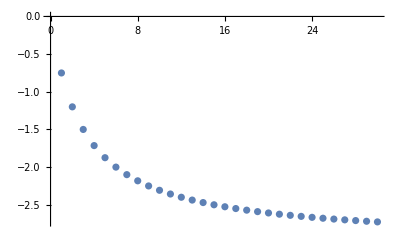

```mathematica
data = Table[n^2/(n+3)-n, {n, 1, 30}];
ListPlot[data]
```

```mathematica
lim_(n->∞) ((n^2-3n+6)/(n^2+5n+1))^(n/2)=lim_(n->∞) (1+(5-8 n)/(1+5 n+n^2))^(n/2)=lim_(n->∞) (1+(5-8 n)/(1+5 n+n^2))^(n/2*(5-8 n)/(1+5 n+n^2)*(1+5 n+n^2)/(5-8 n))=lim_(n->∞) ((1+1/((1+5 n+n^2)/(5-8 n)))^((1+5 n+n^2)/(5-8 n)))^(n/2*(5-8 n)/(1+5 n+n^2))=(*Видим 2ой замечатльный предел*)=lim_(n->∞) ⅇ^(n/2*(5-8 n)/(1+5 n+n^2))=ⅇ^-4
```

```mathematica
ⅇ^-4//N
```

0.0183156

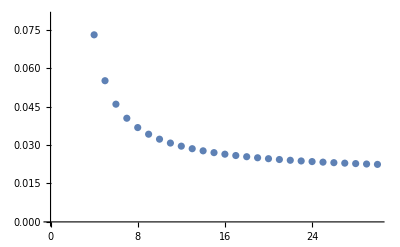

```mathematica
data = Table[((n^2-3n+6)/(n^2+5n+1))^(n/2), {n, 1, 30}];
ListPlot[data]
```

```mathematica
б) lim_(x->0) (1-ln(1+x^(1/3)))^(x/sin^4 x^(1/3))=lim_(x->0) (1-ln(1+x^(1/3)))^(x/( x^(1/3) )^4)=lim_(x->0) (1-ln(1+x^(1/3)))^(x^(-1/3))=lim_(x->0) ⅇ^(x^(-1/3) ln(1-ln(1+x^(1/3))))=lim_(x->0) ⅇ^(- x^(-1/3) ln(1+x^(1/3))) = lim_(x->0) ⅇ^(- x^(-1/3) x^(1/3))=1/ⅇ
```

```mathematica
1/ⅇ//N
```

0.367879

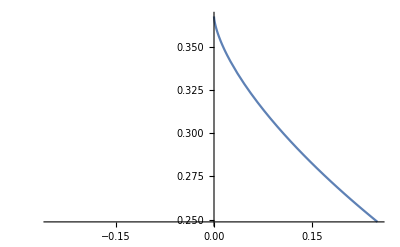

```mathematica
Plot[(1-Log[1+x^(1/3)])^(x/Sin[ x^(1/3)]^4), {x,-1/4, 1/4}]
```

```mathematica
lim_(x->0) ((1+x)^3-(1+3x))/(x+x^5)=lim_(x->0) (x^2 (3+x))/(x(1+x^4))=lim_(x->0) (x (3+x))/(1+x^4)=0
```

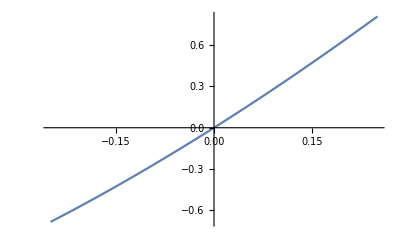

```mathematica
Plot[((1+x)^3-(1+3x))/(x+x^5), {x,-1/4, 1/4}]
```

```mathematica
lim_(x->8) (√(2x+9)-5)/(x^(1/3)-2)=lim_(x->8) (5(√(1+(2x-16)/25)-1))/(2((1+(x-8)/8)^(1/3)-1))=lim_(x->8) (5*1/2*(2x-16)/25)/(2*1/3*(x-8)/8)=(1/5)/(1/3*1/4)=12/5
```

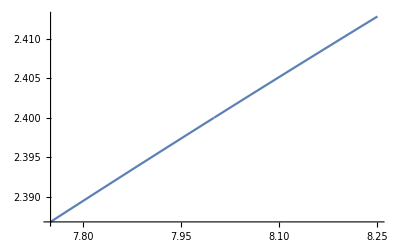

```mathematica
Plot[(√(2x+9)-5)/(x^(1/3)-2), {x,8+-1/4,8+ 1/4}]
```